```mathematica
g[z_]:=z*Log[z^2/(z^2-1)]+Log[(z-1)/(z+1)]
f[z_]:=Log[z^2/(z^2-1)]+1/z Log[(z-1)/(z+1)]
```

```mathematica
a=3+2I;
a=-a
N@g[a]
N@g[Conjugate[a]]
```

-3-2 ⅈ

0.229977-0.157354 ⅈ

0.229977+0.157354 ⅈ

```mathematica
q10=1;
q20=-2;
w=0.2;
l=100;
NIntegrate[1/(Abs[q10]+Abs[q1x])1/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])^2(I*q20+q2x)/(q10^2+w^2*q1x^2)(I*q10+q1x)/(q20^2+w^2*q2x^2)g[I*(q10-q20)-w*(q1x-q2x)],{q1x,-l,l},{q2x,-l,l}]
```

-9.12602×10^-13-1.13186 ⅈ

```mathematica
q10=-1;
q20=2;
w=0.2;
l=1000;
NIntegrate[1/(Abs[q10]+Abs[q1x])1/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])^2(I*q20+q2x)/(q10^2+w^2*q1x^2)(I*q10+q1x)/(q20^2+w^2*q2x^2)g[I*(q10-q20)-w*(q1x-q2x)],{q1x,-l,l},{q2x,-l,l}]
```

3.723×10^-13+1.13187 ⅈ

```mathematica
q10=-1;
q20=2;
w=0.2;
l=1000;
NIntegrate[1/(Abs[q10]+Abs[q1x])1/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])*(Sign[q20]/(Abs[q10]+Abs[q1x])(-w*q2x-I*q20)/(q20^2+w^2 q2x^2)f[I*q10-w*q1x]+Sign[q10]/(Abs[q20]+Abs[q2x])(-w*q1x-I*q10)/(q10^2+w^2 q1x^2)f[I*q20-w*q2x]),{q1x,-l,l},{q2x,-l,l}]
```

-1.11089×10^-11-3.42106 ⅈ

```mathematica
q10=+1;
q20=-2;
w=0.2;
l=100;
NIntegrate[1/(Abs[q10]+Abs[q1x])1/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])*(Sign[q20]/(Abs[q10]+Abs[q1x])(-w*q2x-I*q20)/(q20^2+w^2 q2x^2)f[I*q10-w*q1x]+Sign[q10]/(Abs[q20]+Abs[q2x])(-w*q1x-I*q10)/(q10^2+w^2 q1x^2)f[I*q20-w*q2x]),{q1x,-l,l},{q2x,-l,l}]
```

-1.29237×10^-16-3.42092 ⅈ

```mathematica
w=0.2;
l=100;
zhopa[q10_,q20_]:=NIntegrate[(1/(Abs[q10]+Abs[q1x])2/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])*(Sign[q20]/(Abs[q10]+Abs[q1x])(-w*q2x-I*q20)/(q20^2+w^2 q2x^2)f[I*q10-w*q1x]+Sign[q10]/(Abs[q20]+Abs[q2x])(-w*q1x-I*q10)/(q10^2+w^2 q1x^2)f[I*q20-w*q2x])-1/(Abs[q10]+Abs[q1x])(Sign[q10]-Sign[q20])/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])^2(I*q20+q2x)/(q10^2+w^2*q1x^2)(I*q10+q1x)/(q20^2+w^2*q2x^2)g[I*(q10-q20)-w*(q1x-q2x)])/.{q10->1,q20->-2},{q1x,-l,l},{q2x,-l,l}]
```

```mathematica
zhopa[1,2]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[1/(Abs[q10]+Abs[q1x])2/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])*(Sign[q20]/(Abs[q10]+Abs[q1x])(-w*q2x-I*q20)/(q20^2+w^2 q2x^2)f[I*q10-w*q1x]+Sign[q10]/(Abs[q20]+Abs[q2x])(-w*q1x-I*q10)/(q10^2+w^2 q1x^2)f[I*q20-w*q2x])(*/.{q10->1,q20->-2}*),{q1x,-l,l},{q2x,-l,l}]
```

```mathematica
NIntegrate[(1/(Abs[q10]+Abs[q1x])2/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])*(Sign[q20]/(Abs[q10]+Abs[q1x])(-w*q2x-I*q20)/(q20^2+w^2 q2x^2)f[I*q10-w*q1x]+Sign[q10]/(Abs[q20]+Abs[q2x])(-w*q1x-I*q10)/(q10^2+w^2 q1x^2)f[I*q20-w*q2x])-1/(Abs[q10]+Abs[q1x])(Sign[q10]-Sign[q20])/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])^2(I*q20+q2x)/(q10^2+w^2*q1x^2)(I*q10+q1x)/(q20^2+w^2*q2x^2)g[I*(q10-q20)-w*(q1x-q2x)])/.{q10->1,q20->-2},{q1x,-l,l},{q2x,-l,l}]
```

```mathematica
(1/(Abs[q10]+Abs[q1x])2/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])*(Sign[q20]/(Abs[q10]+Abs[q1x])(-w*q2x-I*q20)/(q20^2+w^2 q2x^2)f[I*q10-w*q1x]+Sign[q10]/(Abs[q20]+Abs[q2x])(-w*q1x-I*q10)/(q10^2+w^2 q1x^2)f[I*q20-w*q2x]))/.{q10->qp+qm,q20->qp-qm}
```

(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))

```mathematica
(1/(Abs[q10]+Abs[q1x])(Sign[q10]-Sign[q20])/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])^2(I*q20+q2x)/(q10^2+w^2*q1x^2)(I*q10+q1x)/(q20^2+w^2*q2x^2)g[I*(q10-q20)-w*(q1x-q2x)])/.{q10->qp+qm,q20->qp-qm}
```

((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))

```mathematica
l=300;
w=0.2;
```

```mathematica
qp=1;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.19781×10^-9-9.45851 ⅈ and 0.000082301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.80504×10^-6-1.916 ⅈ and 0.000172747 for the integral and error estimates.

2.80624×10^-6-7.54251 ⅈ

```mathematica
qp=1/2;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in q2x near {q1x,q2x,qm} = {0.210715,6.28921×10^-9,1.25784×10^-8}. NIntegrate obtained -5.12335×10^-10-28.8658 ⅈ and 0.000160487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.59285×10^-14-7.8346 ⅈ and 0.000236228 for the integral and error estimates.

-5.12319×10^-10-21.0312 ⅈ

```mathematica
qp=1/4;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.34111×10^-11-84.4723 ⅈ and 0.000737532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.63503×10^-11-31.1915 ⅈ and 0.000817564 for the integral and error estimates.

6.97614×10^-11-53.2808 ⅈ

```mathematica
qp=1/8;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.96308×10^-10-234.872 ⅈ and 0.00156734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.82739×10^-14-119.271 ⅈ and 0.00308082 for the integral and error estimates.

-1.9626×10^-10-115.601 ⅈ

```mathematica
qp=1/16;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.54035×10^-10-615.278 ⅈ and 0.00369676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.41126×10^-12-426.91 ⅈ and 0.0087401 for the integral and error estimates.

-7.52624×10^-10-188.368 ⅈ

```mathematica
qp=1/32;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.67112×10^-6-1517.5 ⅈ and 0.0232867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
qp=1/32;
timeTaken=Timing[NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.67112×10^-6-1517.5 ⅈ and 0.0232867 for the integral and error estimates.

```mathematica
timeTaken
```

{41.7188,-2.67112×10^-6-1517.5 ⅈ}

```mathematica
qp=1/128;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.85545×10^-9-7936.5 ⅈ and 0.0443523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.66298×10^-11-11894.6 ⅈ and 0.310588 for the integral and error estimates.

4.90208×10^-9+3958.15 ⅈ

```mathematica
qp=1/256;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.00039×10^-8-17161.2 ⅈ and 0.101464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.40053×10^-10-31465.8 ⅈ and 0.986372 for the integral and error estimates.

-4.93638×10^-8+14304.5 ⅈ

```mathematica
qp=1/1024;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0945873-75250.4 ⅈ and 0.465533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.79388×10^-6-194707. ⅈ and 6.31496 for the integral and error estimates.

-0.0945891+119456. ⅈ

```mathematica
qp=1/512;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

```mathematica
qp=1/2048;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5543.55-145732. ⅈ and 3528.42 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.05093×10^-6-464632. ⅈ and 14.387 for the integral and error estimates.

-5543.55+318900. ⅈ

```mathematica
qp=2;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.56787×10^-8-2.9877 ⅈ and 0.0000336161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.51759×10^-10-0.453559 ⅈ and 0.0000122652 for the integral and error estimates.

2.62304×10^-8-2.53414 ⅈ

```mathematica
qp=3;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06344×10^-9-1.49912 ⅈ and 0.0000203769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.47853×10^-12-0.190349 ⅈ and 5.08246×10^-6 for the integral and error estimates.

2.05996×10^-9-1.30877 ⅈ

```mathematica
qp=20;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.01112×10^-9-0.0512252 ⅈ and 8.98536×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.6235×10^-17-0.00126075 ⅈ and 1.76929×10^-8 for the integral and error estimates.

5.01112×10^-9-0.0499644 ⅈ

```mathematica
qp=50;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.46806×10^-9-0.0085134 ⅈ and 2.29934×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57278×10^-10+0.0000633655 ⅈ and 5.59587×10^-9 for the integral and error estimates.

-8.62534×10^-9-0.00857676 ⅈ

```mathematica
qp=0.0001;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.45634×10^-9-593172. ⅈ and 1.76567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0311736-3.21521×10^6 ⅈ and 109.244 for the integral and error estimates.

0.0311736+2.62204×10^6 ⅈ

```mathematica
qp=0.00001;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000187221-5.19744×10^6 ⅈ and 14.4157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000586672-4.3795×10^7 ⅈ and 978.003 for the integral and error estimates.

-0.00056795+3.85976×10^7 ⅈ

```mathematica
qp=0.0000005;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l},MaxRecursion->50]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00494083-6.00431×10^8 ⅈ and 4960.97 for the integral and error estimates.

0.00494349+5.41014×10^8 ⅈ

1.48977×10^15 and code create is logarithmic Mathematica plot scale scatter the to using with x y your GeoPosition[{42.36,-71.1}] (coordinates:mathematica)

code Copy

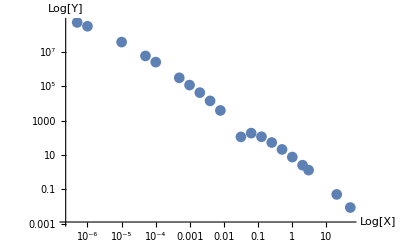

```mathematica
Here is the Mathematica code to create a scatter plot with a logarithmic scale using your x and y coordinates:mathematica
Copy code
(*Define x and y coordinates*)
xCoords={1,1/2,1/4,1/8,1/16,1/32,1/128,1/256,1/1024,1/512,1/2048,2,3,20,50,0.0001,0.00001,0.000001,0.00005,0.0000005};
yCoords={7.542511918741592,21.03124838668479,53.280849509541 ,115.60131239573553,188.36766971083813,113.52111069660964,3958.147143294458 ,14304.549470864906,119456.4265721452 ,43460.91896589336,318900.09086800297,2.534139899702948 ,1.308771407311891,0.049964447849547566,0.008576763532543396,2.6220420009342097*^6,3.8597578103547774*^7 ,3.2402645196835065*^8,6.003295107469017*^6,5.410139604971651*^8 };

(*Combine x and y coordinates into data points*)
data=Transpose[{xCoords,yCoords}];

(*Log-log scatter plot*)
ListLogLogPlot[data,PlotStyle->PointSize[Large],AxesLabel->{"Log[X]","Log[Y]"},PlotMarkers->Automatic,GridLines->Automatic,PlotRange->All]
```

```mathematica
a=3.2402645196835065*^8;
b=5.410139604971651*^8;
N@((Log[a]-Log[b])/(Log[0.000001]-Log[0.0000005]))
```

-0.739554

```mathematica
N@Log[1/256]
Log[14304.549470864906]
```

-5.54518

9.56833

```mathematica
N@Log[1/2048]
Log[318900.09086800297 ]
```

-7.62462

12.6726

```mathematica
(12.672633137940105-9.568332910466395)/(-7.6246189861593985+5.545177444479562)
```

-1.49285

```mathematica
N@Sqrt[2]
```

1.41421

```mathematica
N@Log[50]
Log[0.008576763532543396]
```

3.91202

-4.7587

```mathematica
N@Log[20]
Log[0.049964447849547566]
```

2.99573

-2.99644

```mathematica
(-4.7586986473033805+2.9964435694740144)/(3.912023005428146-2.995732273553991)
```

-1.92325

Ia2

```mathematica
(1/(Abs[q10]+Abs[q1x])1/(Abs[q20]+Abs[q2x])(Abs[q10]+Abs[q20]-Abs[q10+q20])^2/(Abs[q10+q20]+Abs[q1x+q2x])^2 Abs[q10-q20]/((q10-q20)^2+w^2*(q2x-q1x)^2)(1+2*w*(q2x-q1x))/((q10-q20)^2+(q2x*w-q1x*w+1)^2))/.{q10->qp+qm,q20->qp-qm}
```

(2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))

```mathematica
l=300;
w=0.2;
```

```mathematica
qp=1;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.15562 and 0.0000250887 for the integral and error estimates.

0.15562

```mathematica
qp=1/2;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.600519 and 0.000076875 for the integral and error estimates.

0.600519

```mathematica
qp=1/4;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.14694 and 0.000218885 for the integral and error estimates.

2.14694

```mathematica
qp=1/8;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.78951 and 0.000522575 for the integral and error estimates.

6.78951

```mathematica
qp=1/16;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18.8118 and 0.00121723 for the integral and error estimates.

18.8118

```mathematica
qp=1/32;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 46.7392 and 0.00278789 for the integral and error estimates.

46.7392

```mathematica
qp=1/64;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 107.382 and 0.00685283 for the integral and error estimates.

107.382

```mathematica
qp=1/128;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 234.103 and 0.0145427 for the integral and error estimates.

234.103

```mathematica
qp=1/256;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 493.408 and 0.0274715 for the integral and error estimates.

493.408

```mathematica
qp=1/512;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 985.905 and 0.0528782 for the integral and error estimates.

985.905

```mathematica
qp=1/1024;
NIntegrate[((2 (1+2 (-q1x+q2x) w) Abs[qm] (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2)/((4 qm^2+(-q1x+q2x)^2 w^2) (4 qm^2+(1-q1x w+q2x w)^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp]))),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2030.6 and 0.105564 for the integral and error estimates.

2030.6

a^2 and code create is logarithmic Mathematica plot scale scatter the to using with x y your GeoPosition[{42.36,-71.1}] (coordinates:mathematica)

code Copy

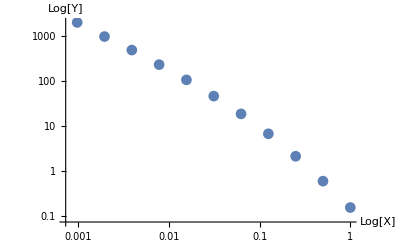

```mathematica
Here is the Mathematica code to create a scatter plot with a logarithmic scale using your x and y coordinates:mathematica
Copy code
(*Define x and y coordinates*)
xCoords={1,1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024};
yCoords={0.1556204889993244,0.6005187474240091,2.1469435105336867,6.7895138557330945,18.811760271906095,46.7391569094016,107.38174465172627,234.10324852742866,493.4084692825786,985.905014127191,2030.5973979792889};

(*Combine x and y coordinates into data points*)
data=Transpose[{xCoords,yCoords}];

(*Log-log scatter plot*)
ListLogLogPlot[data,PlotStyle->PointSize[Large],AxesLabel->{"Log[X]","Log[Y]"},PlotMarkers->Automatic,GridLines->Automatic,PlotRange->All]
```

```mathematica
Log[1]
Log[0.1556204889993244]
```

0

-1.86033

```mathematica
N@Log[1/8]
Log[6.7895138557330945]
```

-2.07944

1.91538

```mathematica
(1.91537934191361-(-1.860334998533))/2.0794415416798357
```

1.81573

```mathematica
N@Log[1/1024]
Log[2030.5973979792889]
```

-6.93147

7.61609

```mathematica
N@Log[1/256]
Log[493.4084692825786]
```

-5.54518

6.20134

```mathematica
(7.61608531346144-6.201337369093009)/(-6.931471805599453+5.545177444479562)
```

-1.02052

Full integral

```mathematica
w=0.2;
l=300;
NIntegrate[NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,Abs[qp],l}],{qp,0.01,l}]
```

NIntegrate::nlim: qm = qp is not a valid limit of integration.

NIntegrate::nlim: qm = Abs[qp] is not a valid limit of integration.

NIntegrate::nlim: qm = qp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

omega dep

```mathematica
w=0.1;
l=300;
```

```mathematica
qp=1/2048/1000;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00169934-4.11651×10^7 ⅈ and 44.9427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.55597×10^8-2.9665×10^9 ⅈ and 35186.7 for the integral and error estimates.

3.55597×10^8+2.92533×10^9 ⅈ

```mathematica
qp=1/512/1000;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000331322-1.28233×10^7 ⅈ and 25.2527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.589561-9.46968×10^8 ⅈ and 20833.1 for the integral and error estimates.

0.589892+9.34144×10^8 ⅈ

```mathematica
a=2.9253311744428463*^9;
b=9.341443843123598*^8;
N@((Log[a]-Log[b])/(Log[1/2048]-Log[1/512]))
```

-0.823441

```mathematica
qp=0.0000001;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l},MaxRecursion->50]-
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (2 («1»)^2 (((-0.2 q2x-ⅈ (1.×10^-8-qm)) (Log[Plus[«3»] Power[«2»]]/(Times[«2»]+Times[«2»])+Log[(«1»)^2/Plus[«1»]]) Sign[1.×10^-8-qm])/((0.04 q2x^2+(1.×10^-8+Times[«2»])^2) (Abs[q1x]+Abs[1.×10^-8+qm]))+((-0.2 q1x-ⅈ («7»+qm)) («1») «1»)/((«1») (Abs[q2x]+Abs[«1»]))))/((2.×10^-8+Abs[q1x+q2x]) (Abs[q2x]+Abs[1.×10^-8-qm]) (Abs[q1x]+Abs[1.×10^-8+qm])) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,3.97545×10^-31},{0,1},{0,1}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.37737×10^9-3.61823×10^10 ⅈ and 3.77871×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

4.77008×10^19 and code create is logarithmic Mathematica plot scale scatter the to using with x y your GeoPosition[{42.36,-71.1}] (coordinates:mathematica)

code Copy

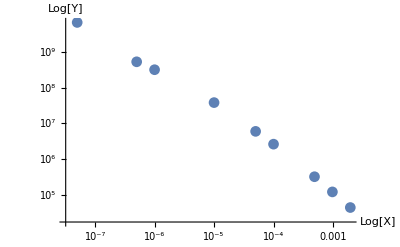

```mathematica
Here is the Mathematica code to create a scatter plot with a logarithmic scale using your x and y coordinates:mathematica
Copy code
(*Define x and y coordinates*)
xCoords={1/1024,1/512,1/2048,0.0001,0.00001,0.000001,0.00005,0.0000005,0.00000005};
yCoords={119456.4265721452 ,43460.91896589336,318900.09086800297,2.6220420009342097*^6,3.8597578103547774*^7 ,3.2402645196835065*^8,6.003295107469017*^6,5.410139604971651*^8 ,6.906575472887409*^9};

(*Combine x and y coordinates into data points*)
data=Transpose[{xCoords,yCoords}];

(*Log-log scatter plot*)
ListLogLogPlot[data,PlotStyle->PointSize[Large],AxesLabel->{"Log[X]","Log[Y]"},PlotMarkers->Automatic,GridLines->Automatic,PlotRange->All]
```

```mathematica
a=6.906575472887409*^9;
b=5.410139604971651*^8;
N@((Log[a]-Log[b])/(Log[0.00000005]-Log[0.0000005]))
```

-1.10605

```mathematica
l=50000;
qp=0.00005;
NIntegrate[(2 (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 (((-ⅈ (-qm+qp)-q2x w) f[ⅈ (qm+qp)-q1x w] Sign[-qm+qp])/(((-qm+qp)^2+q2x^2 w^2) (Abs[q1x]+Abs[qm+qp]))+((-ⅈ (qm+qp)-q1x w) f[ⅈ (-qm+qp)-q2x w] Sign[qm+qp])/(((qm+qp)^2+q1x^2 w^2) (Abs[q2x]+Abs[-qm+qp]))))/((Abs[q1x+q2x]+2 Abs[qp]) (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l},MaxRecursion->50]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2197.61-293255. ⅈ

3.51854×10^11 and code create is logarithmic Mathematica plot scale scatter the to using with x y your GeoPosition[{42.36,-71.1}] (coordinates:mathematica)

code Copy

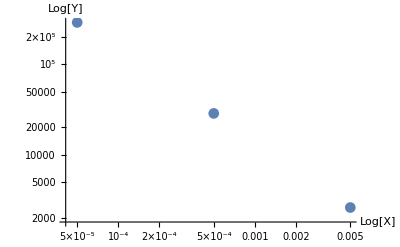

```mathematica
Here is the Mathematica code to create a scatter plot with a logarithmic scale using your x and y coordinates:mathematica
Copy code
(*Define x and y coordinates*)
xCoords={0.0005,0.005,0.00005};
yCoords={28582.83921798822,2580.7296607549997,292126.4385296321};

(*Combine x and y coordinates into data points*)
data=Transpose[{xCoords,yCoords}];

(*Log-log scatter plot*)
ListLogLogPlot[data,PlotStyle->PointSize[Large],AxesLabel->{"Log[X]","Log[Y]"},PlotMarkers->Automatic,GridLines->Automatic,PlotRange->All]
```

```mathematica
a=292126.4385296321;
b=2580.7296607549997;
N@((Log[a]-Log[b])/(Log[0.00005]-Log[0.005]))
```

-1.02691

```mathematica
l=500;
qp=0.001;
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] (-Sign[-qm+qp]+Sign[qm+qp]))/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l},MaxRecursion->100,WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.-204135.8075 ⅈ

```mathematica
3.6547300656428873*^6
```

2.30572×10^11 and code create is logarithmic Mathematica plot scale scatter the to using with x y your GeoPosition[{42.36,-71.1}] (coordinates:mathematica)

code Copy

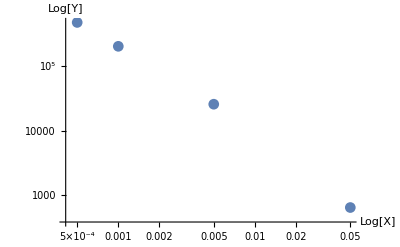

```mathematica
Here is the Mathematica code to create a scatter plot with a logarithmic scale using your x and y coordinates:mathematica
Copy code
(*Define x and y coordinates*)
xCoords={0.005,0.05,0.0005,0.001};
yCoords={25661.610647074893 ,634.1922488237311,480179.4741331039,204135.8075223894857180269};

(*Combine x and y coordinates into data points*)
data=Transpose[{xCoords,yCoords}];

(*Log-log scatter plot*)
ListLogLogPlot[data,PlotStyle->PointSize[Large],AxesLabel->{"Log[X]","Log[Y]"},PlotMarkers->Automatic,GridLines->Automatic,PlotRange->All]
```

```mathematica
a=480179.4741331039;
b=25661.610647074893 ;
N@((Log[a]-Log[b])/(Log[0.0005]-Log[0.005]))
```

-1.27212

```mathematica
l=5000;
qp=0.001;
NIntegrate[((q2x+ⅈ (-qm+qp)) (q1x+ⅈ (qm+qp)) (-2 Abs[qp]+Abs[-qm+qp]+Abs[qm+qp])^2 g[2 ⅈ qm-(q1x-q2x) w] *2)/(((qm+qp)^2+q1x^2 w^2) ((-qm+qp)^2+q2x^2 w^2) (Abs[q1x+q2x]+2 Abs[qp])^2 (Abs[q2x]+Abs[-qm+qp]) (Abs[q1x]+Abs[qm+qp])),{q1x,-l,l},{q2x,-l,l},{qm,qp,l},MaxRecursion->100,WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-35060.7798-48819.66202 ⅈ